# Math 2153

## Photos to surfaces

You press shift - enter to evaluate code.

## Inputting an image

One can directly “paste” an image into Mathematica. Make sure the image is not too large, or else the computations will be too much for your computer.

```mathematica
image=-Graphics-
```

-Graphics-

## Converting an image to a function of several variables

```mathematica
data =ImageData[image];
xPixles=Length[data[[1]]];
yPixles=Length[data];

If[Head[data[[1,1]] ]== List,F[x_,y_]:=First[ImageValue[image,{x,y}]],,F[x_,y_]:=ImageValue[image,{x,y}]]

Plot3D[F[x,y],{x,1,xPixles},{y,1,yPixles},ColorFunction->"GrayTones",PlotPoints->{xPixles-1,yPixles-1},MaxRecursion->0,Mesh->None,BoxRatios->{xPixles, yPixles, Max[xPixles,yPixles]/5}]
```

-Graphics3D-

We can also make contour plots:

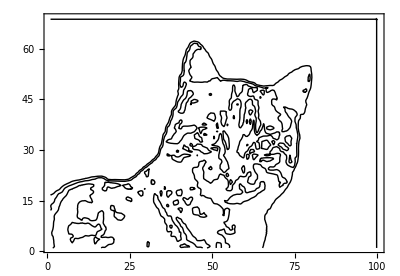

```mathematica
ContourPlot[F[x,y],{x,1,xPixles},{y,1,yPixles},Contours->3,PlotPoints->{xPixles-1,yPixles-1},ContourShading->None,AspectRatio->yPixles/xPixles]
```

## Edge detection via partial derivatives

We’ll numerically compute partial derivatives, use this to find edges of the photo. Note, we’ll be looking at the magnitude of the gradient vector.

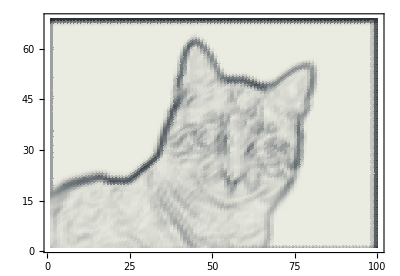

```mathematica
numPartialX[x_,y_]:=(F[x+1,y]-F[x-1,y])/2;
numPartialY[x_,y_]:=(F[x,y+1]-F[x,y-1])/2;

numMagGrad[x_,y_]:=Sqrt[numPartialX[x,y]^2+numPartialY[x,y]^2]

DensityPlot[numMagGrad[x,y],{x,1,xPixles},{y,1,yPixles},MaxRecursion->0,PlotPoints->(xPixles-1),ColorFunction->ColorData[{"GrayTones","Reverse"}],AspectRatio->yPixles/xPixles,PlotRange->All]
```